# Vaje za 2. teden

7. 3. 2024

## Ponovitev

Izračunaj 1+x+x^2+x^3, kjer je x = 1/√e+1/√π, na dva načina: naprej s pomočjo prepisovalnega pravila, nato pa še tako, da definiraš vrednost spremenljivke x.
Spremenljivko x na koncu pobriši.

Ponovitev:

```mathematica
1+x+x^2+x^3 /.{x->1/Sqrt[E]+1/Sqrt[π]}
x=1/Sqrt[E]+1/Sqrt[π];
1+x+x^2+x^3
ClearAll[x]
```

1+1/(√ⅇ)+(1/(√ⅇ)+1/(√π))^2+(1/(√ⅇ)+1/(√π))^3+1/(√π)

```mathematica
1+1/(√ⅇ)+(1/(√ⅇ)+1/(√π))^2+(1/(√ⅇ)+1/(√π))^3+1/(√π)
```

1+1/(√ⅇ)+(1/(√ⅇ)+1/(√π))^2+(1/(√ⅇ)+1/(√π))^3+1/(√π)

## Naloga 1

Izračunaj 1000-i decimalki števil e in π na dva načina:
1. Tako da izračunaš dovolj decimalk obeh števil in pogledaš ustrezno decimalko pri koncu. Zakaj zadnja decimalka ne bo v redu? Uporabi funkcijo N tako, da ji podaš natančnost.
2. Z uporabo funkcije RealDigits in izpisom ustreznega elementa seznama.

```mathematica
N[E,1002] (*1000 bi mi dalo samo 999 decimalk, ker . šteje kot eno decimalko, 1001 pa bi zaokrožilo zadnjo*)
N[π,1002]
RealDigits[E,10,1003][[1]][[1001]]
RealDigits[π,10,1003][[1]][[1001]]
```

2.7182818284590452353602874713526624977572470936999595749669676277240766303535475945713821785251664274274663919320030599218174135966290435729003342952605956307381323286279434907632338298807531952510190115738341879307021540891499348841675092447614606680822648001684774118537423454424371075390777449920695517027618386062613313845830007520449338265602976067371132007093287091274437470472306969772093101416928368190255151086574637721112523897844250569536967707854499699679468644549059879316368892300987931277361782154249992295763514822082698951936680331825288693984964651058209392398294887933203625094431173012381970684161403970198376793206832823764648042953118023287825098194558153017567173613320698112509961818815930416903515988885193458072738667385894228792284998920868058257492796104841984443634632449684875602336248270419786232090021609902353043699418491463140934317381436405462531520961836908887070167683964243781405927145635490613031072085103837505101157477041718986106873969655212671546889570350354

3.14159265358979323846264338327950288419716939937510582097494459230781640628620899862803482534211706798214808651328230664709384460955058223172535940812848111745028410270193852110555964462294895493038196442881097566593344612847564823378678316527120190914564856692346034861045432664821339360726024914127372458700660631558817488152092096282925409171536436789259036001133053054882046652138414695194151160943305727036575959195309218611738193261179310511854807446237996274956735188575272489122793818301194912983367336244065664308602139494639522473719070217986094370277053921717629317675238467481846766940513200056812714526356082778577134275778960917363717872146844090122495343014654958537105079227968925892354201995611212902196086403441815981362977477130996051870721134999999837297804995105973173281609631859502445945534690830264252230825334468503526193118817101000313783875288658753320838142061717766914730359825349042875546873115956286388235378759375195778185778053217122680661300192787661119590921642019894

4

9

Določi še 5., 100. in 443. decimalko.

```mathematica
RealDigits[E,10,447][[1]][[{6,101, 444}]]
RealDigits[π,10,447][[1]][[{6,101, 444}]]
```

{8,4,5}

{9,9,0}

Napiši fuknkcijo, ki sprejme poljubno realno število x in naravno število n in vrne n-to decimalko števila x.

```mathematica
f[x_,n_]:=RealDigits[x,10][[1]][[n+Floor[Log10[x]]+1]]
f[112.345,3]
```

5

## Naloga 2

V Matematico vnesi izraz sin(π/8)+cos(π/8). Kaj Mathematica vrne? Nato poskusi ta izraz poenostaviti s primernim izrazom (končni rezultat se “lepo” izrazi s koreni).Definiraj niz niz, ki bo lepo predstavil in zapisal rešitev te naloge. Po klicu spremenljivke niz naj tako Mathematica izpiše spodnji niz, kjer naj bo niz “___” nadomeščen s pravim rezultatom.
"Vsota sin(π/8) + cos(π/8) je enaka ___."

```mathematica
Sin[π/8]+Cos[π/8]
```

Cos[π/8]+Sin[π/8]

```mathematica
rez=FullSimplify[Sin[π/8]+Cos[π/8]]
```

√(1+1/(√2))

```mathematica
niz:="Vsota sin(π/8) + cos(π/8) je enaka ___."
StringReplace[niz,{"___"->FullSimplify[Sin[π/8]+Cos[π/8]]}]
```

Vsota sin(π/8) + cos(π/8) je enaka ~~√(1+1/(√2))~~.

## Naloga 3

Napiši  funkcijo poenostaviInIzpisi, ki  bo  sprejela  izraz “izr”, ga  poenostavila  in  rezultat  izpisala  v  obliki
“Izraz [izr] se poenostavi v izraz [poenostavljen_izraz]”,
kjer je [izr] nadomestite z vnešenim izrazom, [poenostavljen_izraz] pa s poenostavljenim izrazom.

```mathematica
ClearAll[f[x_],x,niz]
poenostaviInIzpisi[izr_]:=StringForm["Izraz `` se poenostavi v izraz ``.",izr, Simplify[izr]]
poenostaviInIzpisi[(x+1)(x-1)]
```

Izraz (-1+x) (1+x) se poenostavi v izraz -1+x^2.

## Naloga 4

Matej ima 249 jabolk, Jana pa 419 jabolk. Koliko jabolk imata skupaj?
Rešitev zgornje naloge predstavi z nizom, ki ga shrani v spremenljivki niz. Ob klicu spremenljivke niz naj Mathematica vrne:
“Če ima Matej 249 jabolk in Jana 419 jabolk, potem imata skupaj 249 + 419 = 668 jabolk.”
Pomagaj si z vodičem za generiranje nizov (predvsem del za vstavljanje izrazov) in uporabi funkcijo TemplateApply, da definiraš zgornji niz še brez direktnega vnašanja števila 668.

```mathematica
niz="Če ima Matej `jabolk1` jabolk in Jana `jabolk2` jabolk, potem imata skupaj `jabolk1` + `jabolk2` = `jabolk_skupaj` jabolk.";
TemplateApply[niz, <|"jabolk1"->249,"jabolk2"->419,"jabolk_skupaj"->419+249|>]
```

Če ima Matej 249 jabolk in Jana 419 jabolk, potem imata skupaj 249 + 419 = 668 jabolk.

## Naloga 5

1. Definiraj funkcijo f(x)=x^2+3x+2+sin(x).
2. Izračunaj f(3)+f(4).  Uporabi tako prefiksni kot postfiksni način klica funkcije. Rezultat izpiši numerično (kot približek).
3. Nariši graf funkcije f na intervalu [-10,10].
4. Definiraj funkcijo g z istim predpisom kot f, pri čemer g definiraj kot anonimno funkcijo s formalnim parametrom #.
5. Definiraj funkcijo h(x,y)=(f(x)+g(y))^2 na dva načina: na standardni način in kot anonimno funkcijo.

49.3843

49.3843

49.3843

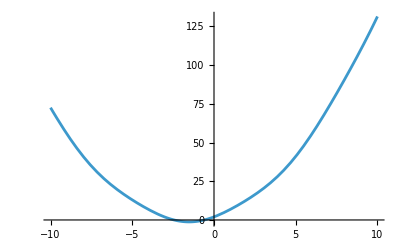

SetDelayed::write: Tag Function in ((f[#1]+g[#2])^2&)[x_,y_] is Protected.

```mathematica
ClearAll[f]
ClearAll[g]
f[x_]:=x^2+3x+2+Sin[x]
N[f[3]+f[4]]
f[3]+f[4]//N (*Nisem ziher ali se s pre in postfliksnim načinom misli to ali kaj drugega*)
(*Pravi nacin:*)((3//f)+(4//f))//N
Plot[f[x],{x,-10,10}]
g = #^2 + 3#+2+Sin[#] &;
h[x_,y_]:=(f[x]+g(y))^2;
h = Power[f[#1] + g[#2], 2]&;
```

## Naloga 6

1. Definiraj funkciji f(x) in g(n), kjer je f(x)=x^3+x+1, g(n) pa je ostanek števila n pri deljenju s 7.
2. Ustvari seznam {f(1),f(2),...,f(100)}. Poišči vsa števila n s tega seznama, za katere je g(n)=3. Uporabi ukaz Select.
3. Poskusi rešiti zgornjo nalogo v eni vrstici s pomočjo uporabe anonimnih funkcij.

```mathematica
ClearAll[g]
f[x_]:=x^3+x+1
g[n_]:=Mod[n,7]
seznam=f[Range[100]]
Select[seznam,g[#]==3&]
Select[Table[x^3+x+1,{x,1,100}],Mod[#,7]==3&]
```

{3,11,31,69,131,223,351,521,739,1011,1343,1741,2211,2759,3391,4113,4931,5851,6879,8021,9283,10671,12191,13849,15651,17603,19711,21981,24419,27031,29823,32801,35971,39339,42911,46693,50691,54911,59359,64041,68963,74131,79551,85229,91171,97383,103871,110641,117699,125051,132703,140661,148931,157519,166431,175673,185251,195171,205439,216061,227043,238391,250111,262209,274691,287563,300831,314501,328579,343071,357983,373321,389091,405299,421951,439053,456611,474631,493119,512081,531523,551451,571871,592789,614211,636143,658591,681561,705059,729091,753663,778781,804451,830679,857471,884833,912771,941291,970399,1000101}

{3,31,521,1011,3391,4931,10671,13849,24419,29823,46693,54911,79551,91171,125051,140661,185251,205439,262209,287563,357983,389091,474631,512081,614211,658591,778781,830679,970399}

{3,31,521,1011,3391,4931,10671,13849,24419,29823,46693,54911,79551,91171,125051,140661,185251,205439,262209,287563,357983,389091,474631,512081,614211,658591,778781,830679,970399}

## Naloga 7

Kaj vrne spodnja koda? Pojasni vsako vrstico!

```mathematica
VsotaKvadratov[x_,y_]:=x^2+y^2
(*Vrne vsoto kvadratov vnešenih števil*)
AplicirajFunkcijo2Spremenljivk[f_,x_,y_]:=f[x,y]
(*vstavi spremenljivki x in y v funkcijo f-> vrne rezultat funkcije na teh spremenljivkah*)
AplicirajFunkcijo2Spremenljivk[VsotaKvadratov,3,4]
(*25*)
```

Zgornja koda vsebuje 3 vrstice. Zapiši ekvivalent te kode z uporabo anonimne funkcije, ki vsebuje le 1 vrstico.

```mathematica
(#1[#2, #3]& )[#1^2+#2^2&,3,4] (*????*)
```

25

## Naloga 8

Nariši graf funkcije f (x, y, z) = x  sin (xy)  cos (xy + z), kjer za z-koordinato uporabi  slider.

```mathematica
f[x_,y_,z_]:=x Sin[x y] Cos[x y+z]
Manipulate[Plot3D[f[x,y,z], {x,-5,5},{y,-5,5}],{z, -5,5}]
```

## Naloga 9

V pomoči si poglej ukaz Join. Definiraj seznam {1,2,...,100,1,2,...,100}. Definiraj še funkcijo DvojniSeznam[n], ki vrne dvojni seznam {1,2,...,n,1,2,...,n}.

```mathematica
Join[Table[x,{x,1,100}],Table[x,{x,1,100}]]
DvojniSeznam[n_]:=Join[Table[n,{n,1,100}],Table[n,{n,1,100}]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

Kaj dela spodnja funkcija?

```mathematica
Krogi[n_]:=Join[{Red},Table[Disk[{2i,0}],{i,n}]]
(*vsakemu od klicov funkcije disk doda še definicijo barve - rdečo, odmik od središča po x aksi se spreminja s spremenljivko 2i *)
```

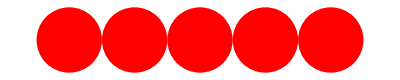

```mathematica
Graphics[Krogi[5]]
```

Definiraj funkcijo NarisiKroge[n], ki nariše n rdečih krogov. Barve lahko definiraš tudi drugače, uporabi domišljijo. Pomagaj si s funkcijo Graphics. Na primer, klic NarisiKroge[5] naj vrne nekaj takega kot:

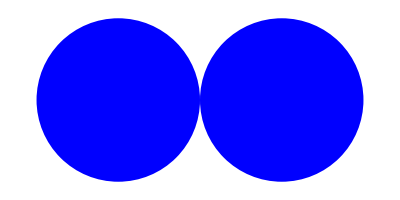

```mathematica
Krogi[n_]:=Graphics[Join[
{Blue},
Table[Disk[{2i,0}],
{i,n}]
]
]
Krogi[2]
```

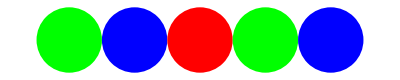
Za dodatni izziv poskusi napisati funkcijo MesaniKrogi[n], ki bo narisala kroge v izmenjajočih barvah. Na primer:
-Graphics-

```mathematica
MesaniKrogi[n_]:=Graphics[Join[
{Green,Blue,Red},
Table[Disk[{2i,0}],
{i,n}]
]
]
MesaniKrogi[3]
```

-Graphics-

Na podoben način definiraj še funkcijo NarisiKrogle[n], ki nariše n sfer. Sfere lahko postaviš tudi drugače (ne nujno v ravni vrsti).

Nariši interaktivni 3d graf, ki vsebuje tri zaporedne krogle, vsaki od katerih lahko spreminjaš njeno drugo koordinato.

-Graphics3D-

```mathematica
Krogle[n_]:=Graphics3D[Join[
{Blue},
Table[Sphere[{2i,0,0}],
{i,n}]
]
]
Krogle[2]
```

-Graphics3D-

```mathematica
InteraktivneKrogle[n_]:=
Manipulate[
Graphics3D[{
Sphere[{0,y1,0},π-1],
Sphere[{4,y2,4},π],
Sphere[{8,y3,8},π-1]
}],
{y1,-10,10},
{y2,-10,10},
{y3,-10,10}
]



InteraktivneKrogle[2]
```

## Naloga 10

Napiši funkcijo, ki sprejme narvni števili m in n in vrne seznam prvih n členov Collatzovega zaporedja za število m. Pomagaj si s funkcijo “RecurrenceTable”.

```mathematica
Collatz[m_,n_]:=Seznam={},
For[i=0, i<n,
If[Mod[m,2]==1,
m//=2,
m=n*3+1
],
Join[Seznam,{m}];
],
Seznam

Collatz[6,7]
```

Syntax::tsntxi: "Collatz[m_,n_]:=Seznam=Table[0,0],For[i=0,i<n,If[«1»],Join[Seznam,{m}];],Seznam" is incomplete; more input is needed.